```mathematica
Clear["Global`*"];
```

## Steady state solution

```mathematica
Clear["Global`*"]
```

```mathematica
s[r_]:= (sr*Rcell)/r Exp[- (r-Rcell)/λ];
sr = η/(4π Rcell^2)γ/λ 1/(1+λ/Rcell);
λ=Sqrt[d/γ];
s[r]
```

(ⅇ^(-(r-Rcell)/(√(d/γ))) γ η)/(4 π r Rcell (1+(√(d/γ))/Rcell) √(d/γ))

```mathematica
FullSimplify[1/r^2 D[ r^2 D[s[r], r], r]*d - γ s[r] ]
```

0

Directly solve differential equation

```mathematica
sol=DSolve[ {0 == d/r^2 D[r^2  D[S[r], r], r] - γ S[r]+ η/(4π Rcell^2)DiracDelta[r-Rcell], S'[Rcell]==η} /. {Rcell-> 1}, S[r], {r, 1, ∞}];
FullSimplify[S[r] /. sol[[1]]] /. {C[1]-> 0}
```

-((ⅇ^(-(2+r) √(γ/d)) (4 d^2 ⅇ^((1+2 r) √(γ/d)) π √(γ/d) η+d ⅇ^((1+2 r) √(γ/d)) √(γ/d) η DiracDelta'[0]))/(4 d π r (-γ+d √(γ/d))))

```mathematica
sol=DSolve[ {0 == d/r^2 D[r^2  D[S[r], r], r] - γ S[r], 2S'[Rcell]/Rcell + S''[Rcell]==η/(4π Rcell^2)} , S[r], {r, 1, ∞}];
```

```mathematica
FullSimplify[S[r] /. sol[[1]]  /. {√(γ/d)->λ} /.{C[1]-> (d ⅇ^(Rcell λ) η)/(4 π Rcell γ)}]
```

(d ⅇ^((-r+Rcell) λ) η)/(4 π r Rcell γ)

```mathematica
s[r_]:=(d ⅇ^((-r+Rcell) λ) η)/(4 π r Rcell γ);
FullSimplify[1/r^2 D[ r^2 D[s[r], r], r]*d - γ s[r] ] /. {λ-> √(γ/d)}
```

0

## Dynamical solution

```mathematica
Piecewise[{{1,Rcell<r≤Rcell+dR},{0,True}}]
```

```mathematica
rmax = 10;
tmax = 10;
Rcell = 1; dR = 0.1;
d=10;
γ=1;
η= 10*4π;
sol=NDSolve[ {D[S[r,t], t] == d/r^2 D[r^2  D[S[r,t], r], r] - γ S[r,t]+ η/(4π Rcell^2)DiracDelta[r-Rcell],  S[r,0] ==0,S[rmax,t]==0,Derivative[1,0][S][Rcell,t]==η}, S, {r, Rcell, rmax}, {t,0,tmax}];
S[r,t] /. sol[[1]]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

InterpolatingFunction[{{1., 10.}, {0., 10.}}, <>][r,t]

```mathematica
Plot3D[Evaluate[S[r,t]/. First[sol]],{t,0,tmax},{r,0,rmax}, PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.000715, 0.000715} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

```mathematica
Manipulate[Plot[S[r,t] /. sol[[1]] /. {t-> tm}, {r,Rcell,rmax}, AxesOrigin-> {1,0}, PlotRange-> {Automatic, {-0.05,0.5}}], {tm,0,tmax}]
```

NDSolve::dsvar: 1.00018 cannot be used as a variable.

ReplaceAll::reps: SuperscriptBox[« 3 » is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[« 2 »« 1 » is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 1.18386 cannot be used as a variable.

NDSolve::dsvar: 1.36753 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

NDSolve::dsvar: 1.00018 cannot be used as a variable.

ReplaceAll::reps: SuperscriptBox[« 3 » is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[« 2 »False is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: SuperscriptBox[« 1 »« 1 »False is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 1.18386 cannot be used as a variable.

NDSolve::dsvar: 1.36753 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

Plot::plln: Limiting value Rcell in {r, Rcell, rmax} is not a machine-sized real number.

## Solution from Fourier transform

```mathematica
c0[q_]:= Integrate[(r*f[r]-(η R)/(2 π λ γ)Exp[(R-r)/λ])*Exp[-I q r], {r,0,∞}];
c0[q]
```

∫_0^∞ ⅇ^(-ⅈ q r) (-(ⅇ^((-r+R)/λ) R η)/(2 π γ λ)+r f[r])ⅆr

```mathematica
c[t_, r_]:= 1/(2π r)Integrate[ cq0*Exp[I q r - (λ q^2+1)γ t], {q,-∞,∞}, Assumptions-> {λ ∈ Reals, γ∈ Reals, t∈ Reals, λ>0, γ>0, t>0}] + (η R)/(2π λ γ r)Exp[(R-r)/λ];
ctr = c[t,r]
```

(ⅇ^((-r+R)/λ) R η)/(2 π r γ λ)+(cq0 ⅇ^(-t γ-r^2/(4 t γ λ)))/(2 √π r √(t γ λ))

```mathematica
params = {λ-> 1,R-> 1, γ-> 1, η-> 1, f[r]->0}; 
cq=Simplify[c0[q] /. params, Assumptions-> {q∈ Reals}]
```

(ⅈ ⅇ)/(2 π (-ⅈ+q))

```mathematica
ctr  /. params /. {cq0 -> cq, t-> 1, r-> 2}
```

1/(4 ⅇ π)-ⅇ^(-2-ⅈ q)/(4 √π (2 π+2 ⅈ π q))

## Using Laplace transforms

```mathematica
InverseLaplaceTransform[(η(2 r+R))/(-d q^2 + γ)(1-Exp[(d q^2 - γ) t]) /. {d-> 1, γ-> 1},q,r ]
```

(2 r+R) η InverseLaplaceTransform[(1-ⅇ^((-1+q^2) t))/(1-q^2),q,r]

## Interaction strengths

```mathematica
Integrate[R Exp[R-r]/r /. {r-> Sqrt[x^2+y^2+z^2]}, {x,y,z} ∈ Sphere[{0,0,d}, R], Assumptions-> {R>0} ]
```

$Aborted

```mathematica
Integrate[Exp[R-r]/r  /. {r-> Sqrt[d^2+R^2+ 2R Cos[ϕ]Sin[ϕ]]}, {ϕ,0,π}, Assumptions-> {R>0, d>R}]
```

$Aborted

```mathematica
Integrate[Exp[-y]/Sqrt[R^2 - (y^2-d^2-R^2)^2], {y, Sqrt[d^2+R^2],Sqrt[d^2+R^2+R]}, Assumptions-> {R>0, d>0, d>R}]
```

Integrate[ⅇ^-y/(√(R^2-(-d^2-R^2+y^2)^2)),{y,√(d^2+R^2),√(d^2+R+R^2)},Assumptions→{R>0,d>0,d>R}]

```mathematica
ρ[z_]:=Sqrt[R^2-z^2];
```

```mathematica
Integrate[ρ[z]*Sqrt[1-ρ'[z]^2]*Exp[-Sqrt[(z-d)^2+ρ[z]^2]]/Sqrt[(z-d)^2+ρ[z]^2], {z,-R,R}, Assumptions-> {R>0, d>R}]
```

```mathematica
Integrate[ρ[z]*Sqrt[1-ρ'[z]^2]/.{R->1},{z,-1,1}]
```

ⅈ+ArcSin[√2]/(√2)

## Integrate over sphere (cylindrical coordinates)

```mathematica
ρ[z_]:=Sqrt[R^2-z^2];
Norm@Cross[{ρ'[z] Cos[θ],ρ'[z]Sin[θ], 1},{-ρ[z] Sin[θ], ρ[z] Cos[θ], 0}] // FullSimplify
```

√(Abs[z]^2+Abs[R-z] Abs[R+z] (Abs[Cos[θ]]^2+Abs[Sin[θ]]^2))

```mathematica
Integrate[√(z^2+(R-z) (R+z)) ,{θ,0,2π}, {z,-1,1}, Assumptions-> {R>0}]
```

4 π R

```mathematica
Integrate[Exp[-Sqrt[(z-d)^2+ρ[z]^2]]/Sqrt[(z-d)^2+ρ[z]^2]*√(z^2+(R-z) (R+z)),{θ,0,2π}, {z,-R,R}, Assumptions-> {R>0,d>0, d>R}]//Simplify
```

(4 ⅇ^-d π R Sinh[R])/d

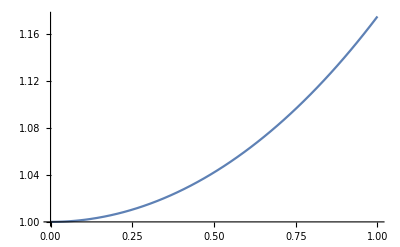

```mathematica
Plot[Sinh[x]/x,{x,0,1}, PlotRange-> All]
```